Data options

```mathematica
EarlyOrLate="Early";(*Early,Late,or All*)
BeamNoBeam = "Beam";
subtract1point5=True;
```

```mathematica
Dst=-20;
dstStr=If[Dst==0,"","-Dst"<>ToString[Dst]];
```

```mathematica
ventileOrDecile = "ventile";
GoverK=5;
GoverKStr=(Switch[ToUpperCase[ventileOrDecile],"VENTILE","Ven","DECILE","Dec"])<>ToString[GoverK];
```

```mathematica
dateStr="20180512-";
dateStr="20180514-";
```

```mathematica
earlyMLTStr = "20_50-22_25MLT";
lateMLTStr = "22_25-1_50MLT";
```

```mathematica
earlyMLTStr = "20_50-23MLT";
lateMLTStr = "23-1_50MLT";
```

Setup input files

```mathematica
inDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/txtOutput/";
```

```mathematica
earlyNames={dateStr<>earlyMLTStr<>"-ionBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv",
dateStr<>earlyMLTStr<>dstStr<>"-noBeam-data-allALT-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv"};
```

```mathematica
lateNames={dateStr<>lateMLTStr<>"-ionBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv",
dateStr<>lateMLTStr<>dstStr<>"-noBeam-data-allALT-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv"};
```

```mathematica
allNames={dateStr<>"20_50-1_50MLT"<>"-ionBeam-data-allALT"<>dstStr<>"-NORTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv",
dateStr<>"20_50-1_50MLT"<>dstStr<>"-noBeam-data-allALT-NORTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv"};
```

### Read in array of kappa values

```mathematica
Switch[ToUpperCase[EarlyOrLate],
"EARLY",
names=earlyNames;,
"LATE",
names=lateNames;,
"ALL",
names=allNames;
]
```

```mathematica
Switch[BeamNoBeam//ToUpperCase,
"BEAM",
fName=names[[1]];,
"NOBEAM",
fName=names[[2]];
]
```

```mathematica
data=Import[inDir<>fName]//Flatten;
```

```mathematica
If[subtract1point5,subVal=1.5,subVal=0];
```

```mathematica
data=data-subVal;
plotMin=1.5-subVal;
plotMax=20;
```

Now check ‘er out

```mathematica
this=SmoothKernelDistribution[data]
```

DataDistribution[…]

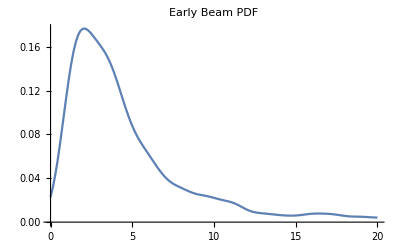
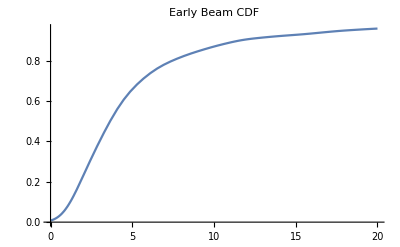

```mathematica
Table[Plot[f[this,x],{x,plotMin,plotMax},PlotLabel->(EarlyOrLate<>" "<>BeamNoBeam<>" "<>ToString[f])],{f,{PDF,CDF}}]
```

```mathematica
fitData=Select[data,#≤ 100&];
```

```mathematica
candidateDists=FindDistribution[fitData,3,PerformanceGoal->"Quality"]
```

{FrechetDistribution[1.93821,3.78161,-1.13656],ParetoDistribution[7.,2.03851,0.700751,-0.0262314],WeibullDistribution[0.96381,5.79248,-0.0262314]}

```mathematica
(*strippedCandidates=((candidateDists[[#]])[[2]])[[1]]&/@{1,2,3};*)
```

```mathematica
strippedCandidates=(If[ToString[Head[candidateDists[[#]]]]=="MixtureDistribution",((candidateDists[[#]])[[2]])[[1]],candidateDists[[#]]])&/@Range[Length@candidateDists];
```

```mathematica
IGParms=FindDistributionParameters[fitData,InverseGaussianDistribution[μ,λ]];
```

```mathematica
strippedCandidates=strippedCandidates~Join~{InverseGaussianDistribution[μ,λ]/.IGParms}
```

{FrechetDistribution[1.93821,3.78161,-1.13656],ParetoDistribution[7.,2.03851,0.700751,-0.0262314],WeibullDistribution[0.96381,5.79248,-0.0262314],InverseGaussianDistribution[5.68401,2.05774]}

#### A new go

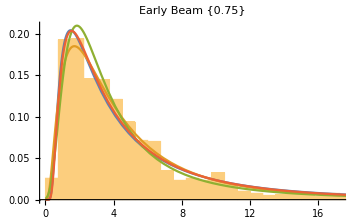
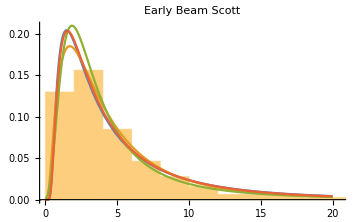
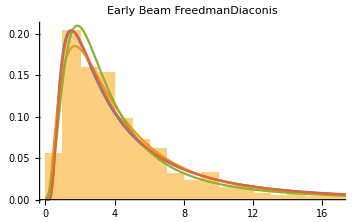
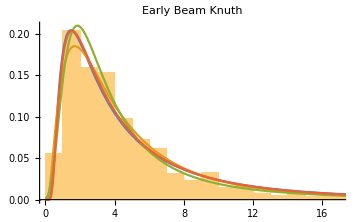
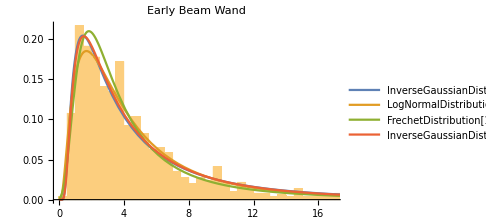

```mathematica
Table[plotLegends=If[ToString[bins]=="Wand",(ToString[#]& /@ strippedCandidates),None];
Show[
Histogram[data,bins,"PDF",PlotLabel->(EarlyOrLate<>" "<>BeamNoBeam<>" "<>ToString[bins]),ImageSize->Medium],Plot[Evaluate[PDF[#,x]&/@ strippedCandidates],{x,plotMin,plotMax},PlotLegends->plotLegends]],{bins,{{0.75},"Scott","FreedmanDiaconis","Knuth","Wand"}}]
```

```mathematica
{{"Pct < κ=1.5"}~Join~Table[CDF[dist,1.5-subVal]*100,{dist,strippedCandidates}],{"Pct > κ=15"}~Join~Table[(1-CDF[dist,1.5-subVal+15])*100,{dist,strippedCandidates}]}//TableForm
```

Pct < κ=1.5 | 0 | 0 | 0.00680683 | 0
Pct > κ=15 | 6.49201 | 5.10781 | 6.18172 | 5.98985

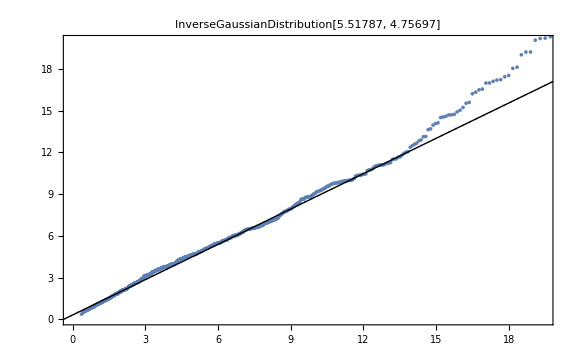
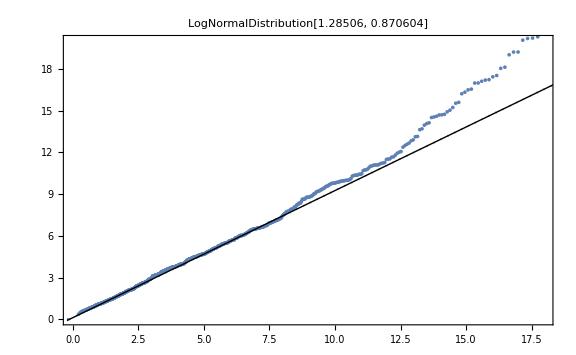
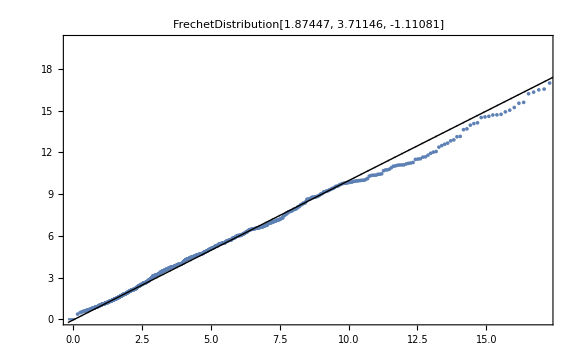
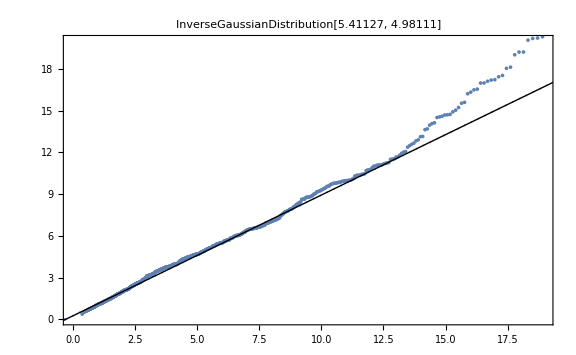

```mathematica
Table[QuantilePlot[data,dist,PlotLabel->ToString[dist],PlotRange->{plotMin,plotMax},ImageSize->Large],{dist,strippedCandidates}]
```

```mathematica
Table[Through[{Mean,Median,(FindMaximum[{PDF[#,x],(1.5-subVal)≤x<7-subVal},{x,(1.5-subVal)}]&)}[dist]],{dist,strippedCandidates~Join~{this}}]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{{4.67942,4.0799,{0.165285,{x→2.83132}}},{4.84435,4.19647,{0.157881,{x→2.84435}}},{7.75889,4.80862,{0.142403,{x→2.66732}}},{8.11923,5.03188,{0.14462,{x→1.97889}}},{8.11923,5.16204,{0.126046,{x→3.38418}}}}

#### EB

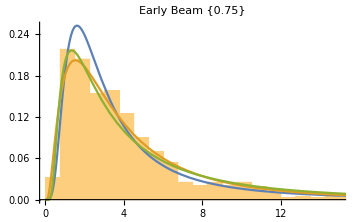
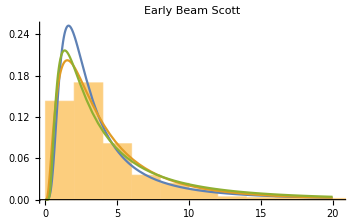
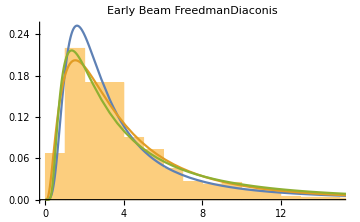
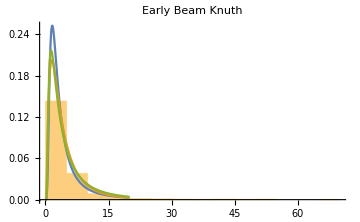
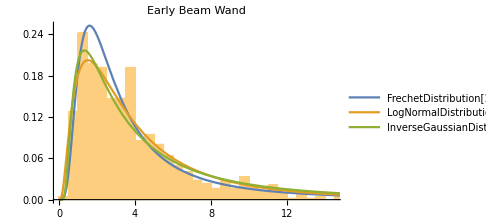

```mathematica
Table[plotLegends=If[ToString[bins]=="Wand",(ToString[#]& /@ strippedCandidates),None];
Show[
Histogram[data,bins,"PDF",PlotLabel->(EarlyOrLate<>" "<>BeamNoBeam<>" "<>ToString[bins]),ImageSize->Medium],Plot[Evaluate[PDF[#,x]&/@ strippedCandidates],{x,plotMin,plotMax},PlotLegends->plotLegends]],{bins,{{0.75},"Scott","FreedmanDiaconis","Knuth","Wand"}}]
```

```mathematica
Table[CDF[dist,1.5-subVal]*100,{dist,strippedCandidates}]
```

{7.65829×10^-6,0,0}

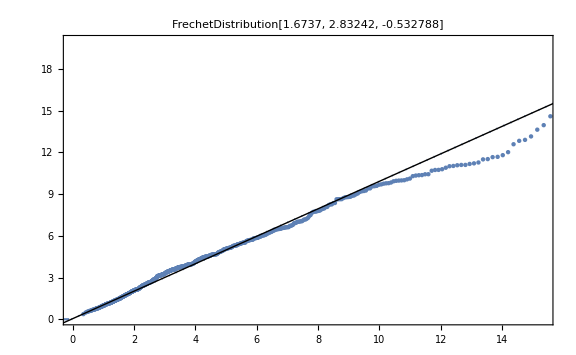
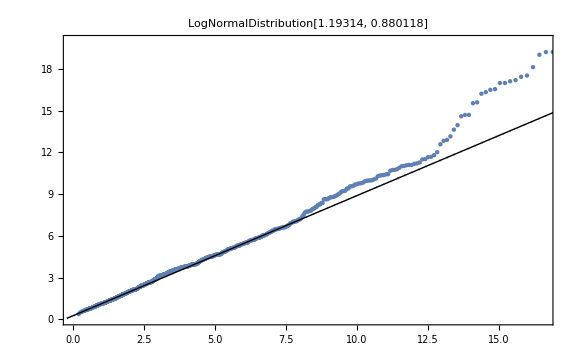
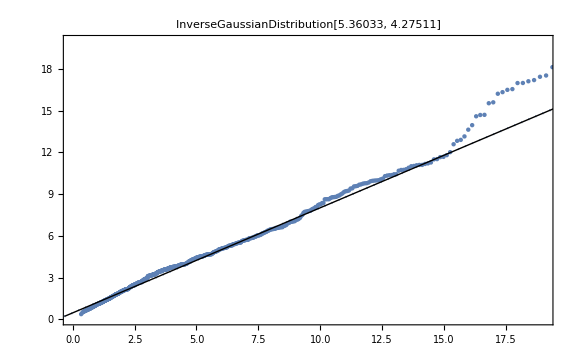

```mathematica
Table[QuantilePlot[data,dist,PlotLabel->ToString[dist],PlotRange->{plotMin,plotMax},ImageSize->Large],{dist,strippedCandidates}]
```

```mathematica
Table[Through[{Mean,Median,(FindMaximum[{PDF[#,x],(1.5-subVal)≤x<7-subVal},{x,(1.5-subVal)}]&)}[dist]],{dist,strippedCandidates~Join~{this}}]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{{5.38833,2.9538,{0.252217,{x→1.60487}}},{4.67959,3.21347,{0.208517,{x→1.51534}}},{5.06876,3.23626,{0.224268,{x→1.32793}}},{5.01765,3.28644,{0.194296,{x→1.83506}}}}

#### LB

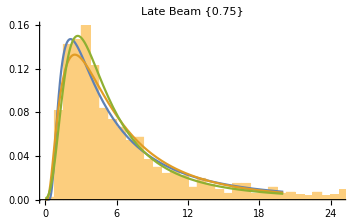
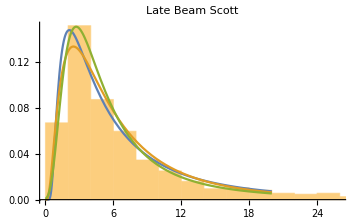
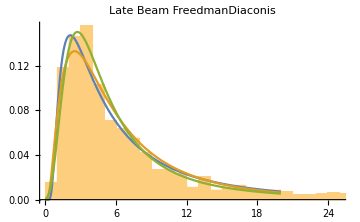
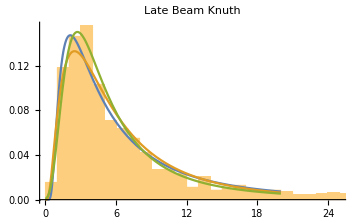
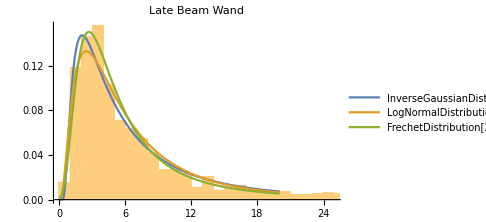

```mathematica
Table[plotLegends=If[ToString[bins]=="Wand",(ToString[#]& /@ strippedCandidates),None];
Show[
Histogram[data,bins,"PDF",PlotLabel->(EarlyOrLate<>" "<>BeamNoBeam<>" "<>ToString[bins]),ImageSize->Medium],Plot[Evaluate[PDF[#,x]&/@ strippedCandidates],{x,plotMin,plotMax},PlotLegends->plotLegends]],{bins,{{0.75},"Scott","FreedmanDiaconis","Knuth","Wand"}}]
```

```mathematica
Table[CDF[dist,1.5-subVal]*100,{dist,strippedCandidates}]
```

{0,0,0.00662298}

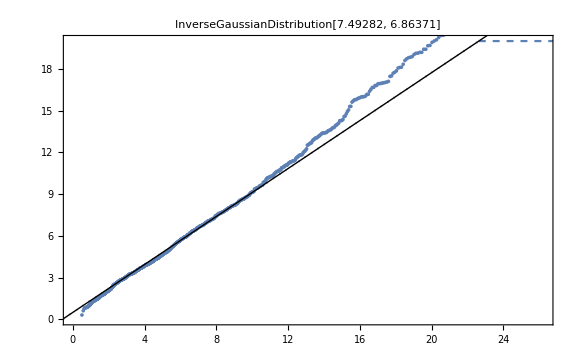
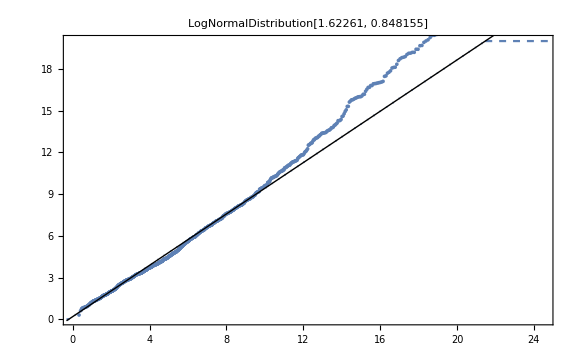
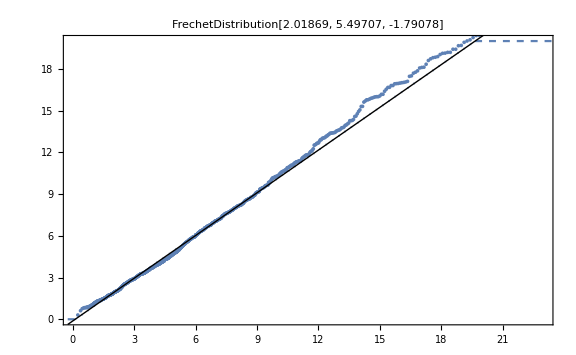

```mathematica
Table[QuantilePlot[data,dist,PlotLabel->ToString[dist],PlotRange->{plotMin,plotMax},ImageSize->Large],{dist,strippedCandidates}]
```

```mathematica
Table[Through[{Mean,Median,(FindMaximum[{PDF[#,x],(1.5-subVal)≤x<7-subVal},{x,(1.5-subVal)}]&)}[dist]],{dist,strippedCandidates~Join~{this}}]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{{7.49282,4.92112,{0.147304,{x→2.10699}}},{7.25937,5.06629,{0.133031,{x→2.46759}}},{7.86486,4.80068,{0.150252,{x→2.71288}}},{7.29017,4.75353,{0.141161,{x→3.07238}}}}

#### EN

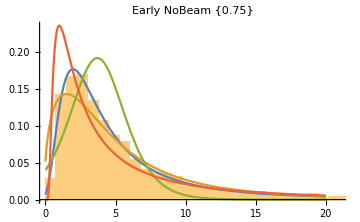
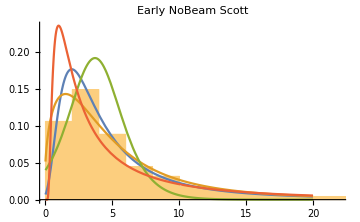
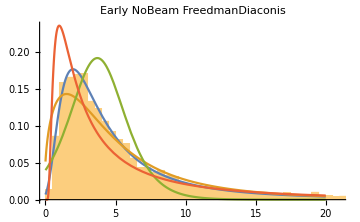
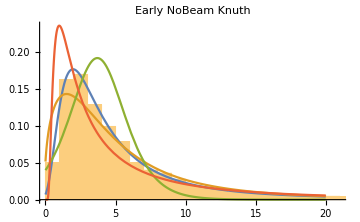
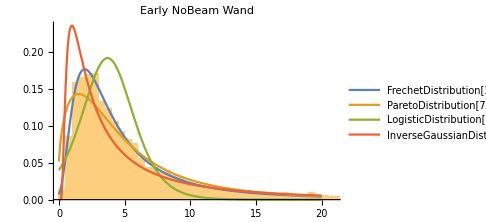

```mathematica
Table[plotLegends=If[ToString[bins]=="Wand",(ToString[#]& /@ strippedCandidates),None];
Show[
Histogram[data,bins,"PDF",PlotLabel->(EarlyOrLate<>" "<>BeamNoBeam<>" "<>ToString[bins]),ImageSize->Medium],Plot[Evaluate[PDF[#,x]&/@ strippedCandidates],{x,plotMin,plotMax},PlotLegends->plotLegends]],{bins,{{0.75},"Scott","FreedmanDiaconis","Knuth","Wand"}}]
```

```mathematica
Table[CDF[dist,1.5-subVal]*100,{dist,strippedCandidates}]
```

{0.080131,0.25153,5.51158,0}

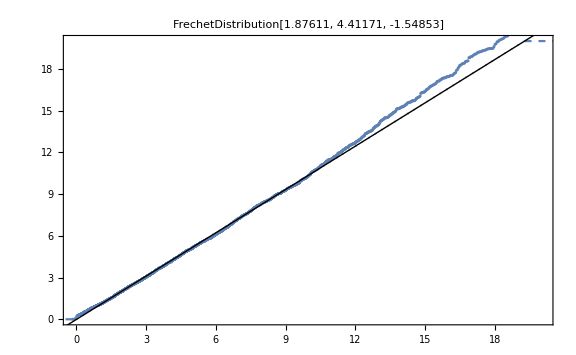
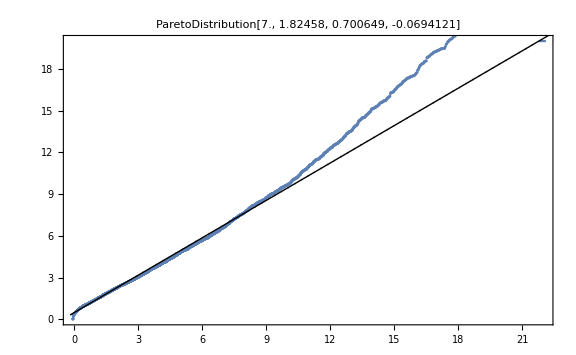
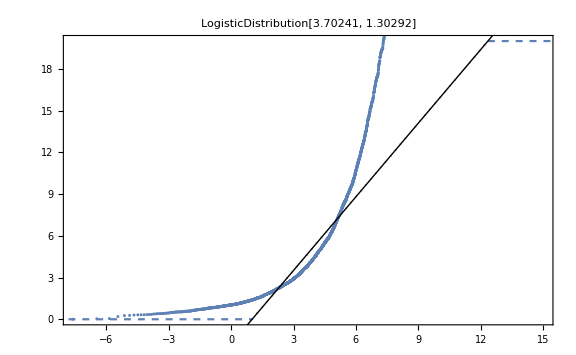
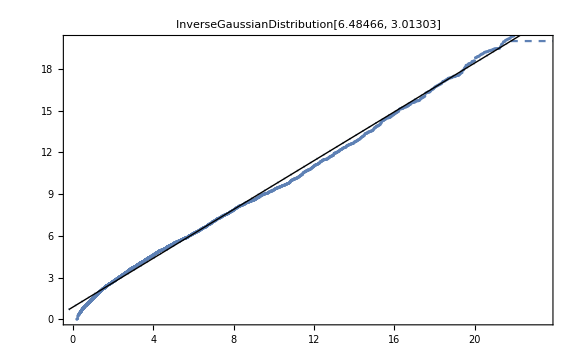

```mathematica
Table[QuantilePlot[data,dist,PlotLabel->ToString[dist],PlotRange->{plotMin,plotMax},ImageSize->Large],{dist,strippedCandidates}]
```

```mathematica
Table[Through[{Mean,Median,(FindMaximum[{PDF[#,x],(1.5-subVal)≤x<7-subVal},{x,(1.5-subVal)}]&)}[dist]],{dist,strippedCandidates~Join~{this}}]
```

Power::infy: Infinite expression 1/0. encountered.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{{6.81814,3.81499,{0.176733,{x→1.96471}}},{6.31902,4.00642,{0.143187,{x→1.50173}}},{3.70241,3.70241,{0.191877,{x→3.70241}}},{6.48466,3.21827,{0.235772,{x→0.981342}}},{6.48466,3.96382,{0.162479,{x→2.25567}}}}

#### LN

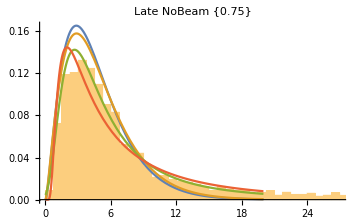
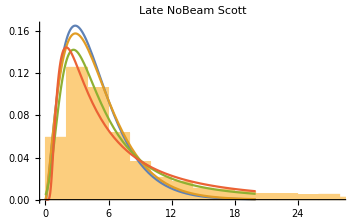
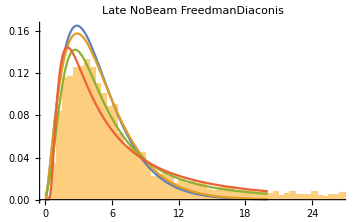
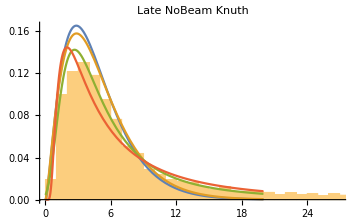
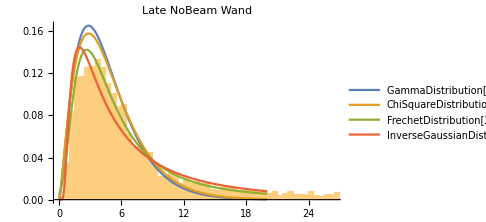

```mathematica
Table[plotLegends=If[ToString[bins]=="Wand",(ToString[#]& /@ strippedCandidates),None];
Show[
Histogram[data,bins,"PDF",PlotLabel->(EarlyOrLate<>" "<>BeamNoBeam<>" "<>ToString[bins]),ImageSize->Medium],Plot[Evaluate[PDF[#,x]&/@ strippedCandidates],{x,plotMin,plotMax},PlotLegends->plotLegends]],{bins,{{0.75},"Scott","FreedmanDiaconis","Knuth","Wand"}}]
```

```mathematica
Table[CDF[dist,1.5-subVal]*100,{dist,strippedCandidates}]
```

{0,0,0.0690467,0}

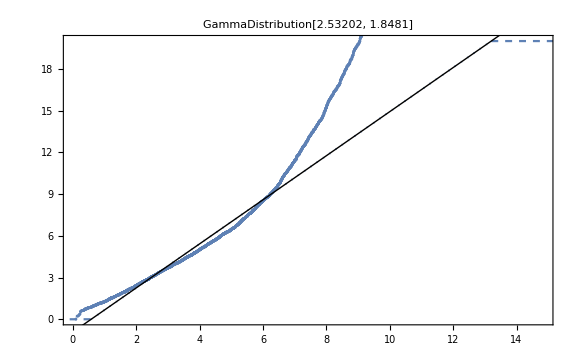
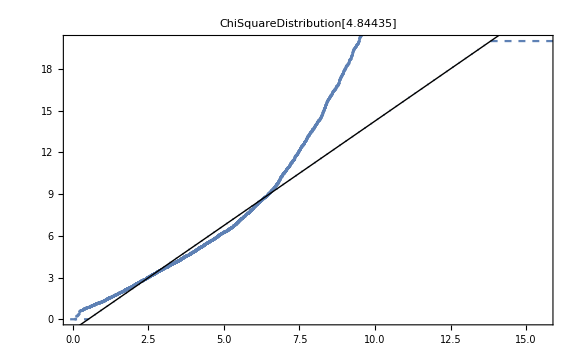
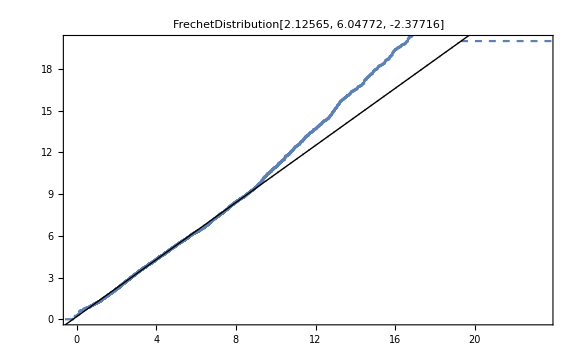
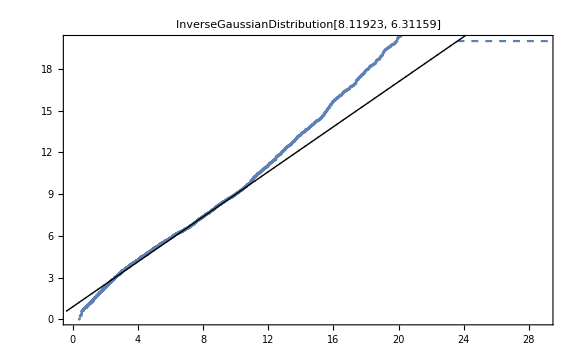

```mathematica
Table[QuantilePlot[data,dist,PlotLabel->ToString[dist],PlotRange->{plotMin,plotMax},ImageSize->Large],{dist,strippedCandidates}]
```

```mathematica
Table[Through[{Mean,Median,(FindMaximum[{PDF[#,x],(1.5-subVal)≤x<7-subVal},{x,(1.5-subVal)}]&)}[dist]],{dist,strippedCandidates~Join~{this}}]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{{4.67942,4.0799,{0.165285,{x→2.83132}}},{4.84435,4.19647,{0.157881,{x→2.84435}}},{7.75889,4.80862,{0.142403,{x→2.66732}}},{8.11923,5.03188,{0.14462,{x→1.97889}}},{8.11923,5.16204,{0.126046,{x→3.38418}}}}